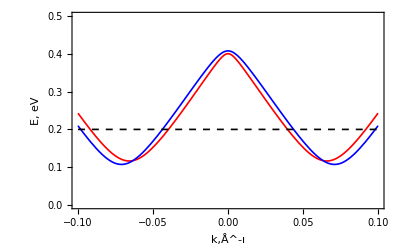

```mathematica
t=0.4;   c=6.25;
f1[x_,U_,d_]:=Sqrt[U^2+d^2+(c*x)^2+t^2+2*(U^2*(d^2+(c*x)^2)+t^2*(c*x)^2)^(1/2)];
f2[x_,U_,d_]:=Sqrt[U^2+d^2+(c*x)^2+t^2-2*(U^2*(d^2+(c*x)^2)+t^2*(c*x)^2)^(1/2)];
f3[x_,U_,d_]:=-Sqrt[U^2+d^2+(c*x)^2+t^2+2*(U^2*(d^2+(c*x)^2)+t^2*(c*x)^2)^(1/2)];
f4[x_,U_,d_]:=-Sqrt[U^2+d^2+(c*x)^2+t^2-2*(U^2*(d^2+(c*x)^2)+t^2*(c*x)^2)^(1/2)];

Plot[{f2[x,0.1,0.12],f2[x,0.2,0.12],0.2},{x,-0.1,0.1},FrameLabel->{"k,Å^-ı","E, eV"},PlotRange->{0,0.5},PlotStyle->{{Thickness[0.003],Red},{Thickness[0.003],Blue},{Thickness[0.003],Dashed,Black}},Frame->True]
```

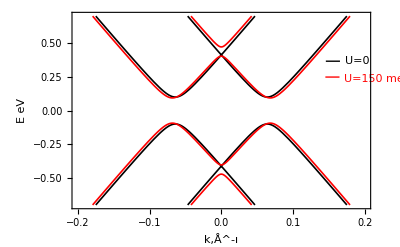

-Graphics-

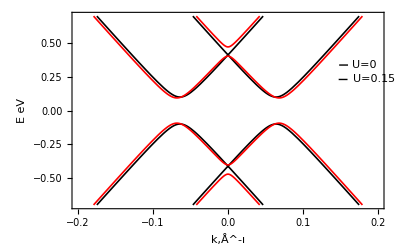

```mathematica
q1[x_,U_,d_]:=Sqrt[U^2+d^2+(c*x)^2+t^2+2*(U^2*(d^2+(c*x)^2)+t^2*(c*x)^2+d^2*t^2)^(1/2)];
q2[x_,U_,d_]:=-Sqrt[U^2+d^2+(c*x)^2+t^2+2*(U^2*(d^2+(c*x)^2)+t^2*(c*x)^2+d^2*t^2)^(1/2)];
q3[x_,U_,d_]:=Sqrt[U^2+d^2+(c*x)^2+t^2-2*(U^2*(d^2+(c*x)^2)+t^2*(c*x)^2+d^2*t^2)^(1/2)];
q4[x_,U_,d_]:=-Sqrt[U^2+d^2+(c*x)^2+t^2-2*(U^2*(d^2+(c*x)^2)+t^2*(c*x)^2+d^2*t^2)^(1/2)];
Plot[{q1[x,0],q2[x,0],q3[x,0],q4[x,0],q1[x,0.15],q2[x,0.15],q3[x,0.15],q4[x,0.15]},{x,-0.2,0.2},FrameLabel->{"k,Å^-ı","E,eV"},PlotRange->{-0.7,0.7},PlotStyle->{{Thickness[0.003],Black},{Thickness[0.003],Black},{Thickness[0.003],Black},{Thickness[0.003],Black},{Thickness[0.003],Red},{Thickness[0.003],Red},{Thickness[0.003],Red},{Thickness[0.003],Red}},Frame->True]
```

-Graphics-

```mathematica
Manipulate[Plot[{f2[x,0.1,d],f2[x,0.2,d],0.2},{x,-0.2,0.2},PlotRange->{0,0.45}],{d,0,0.4}]
```

```mathematica
Manipulate[Plot[{f4[x,U,d],f2[x,U,d]},{x,-0.2,0.2},PlotRange->{-0.6,0.6}],{U,0,0.35},{d,-0.2,0.2}]
```

c", "*", "x"}], ")"}], "2"], "+", 

     SuperscriptBox["t", "2"], "+", 

     RowBox[{"2", "*", 

      SuperscriptBox[

       RowBox[{"(", 

        RowBox[{

         RowBox[{

          SuperscriptBox["U", "2"], "*", 

          RowBox[{"(", 

           RowBox[{

            SuperscriptBox["d", "2"], "+", 

            SuperscriptBox[

             RowBox[{"(", 

              RowBox[{"c", "*", "x"}], ")"}], "2"]}], ")"}]}], "+", 

         RowBox[{

          SuperscriptBox["t", "2"], "*", 

          SuperscriptBox[

           RowBox[{"(", 

            RowBox[{"c", "*", "x"}], ")"}], "2"]}]}], ")"}], 

       RowBox[{"1", "/", "2"}]]}]}], "]"}]}], ";"}], "\[IndentingNewLine]", 

 RowBox[{

  RowBox[{

   RowBox[{"f2", "[", 

    RowBox[{"x_", ",", "U_"}], "]"}], ":=", 

   RowBox[{"Sqrt", "[", 

    RowBox[{

     SuperscriptBox["U", "2"], "+", 

     SuperscriptBox["d", "2"], "+", 

     SuperscriptBox[

      RowBox[{"(", 

       RowBox[{"c", "*", "x"}], ")"}], "2"], "+", 

     SuperscriptBox["t", "2"], "-", 

     RowBox[{"2", "*", 

      SuperscriptBox[

       RowBox[{"(", 

        RowBox[{

         RowBox[{

          SuperscriptBox["U", "2"], "*", 

          RowBox[{"(", 

           RowBox[{

            SuperscriptBox["d", "2"], "+", 

            SuperscriptBox[

```mathematica
dsdd
```